## Wave Packet

### Non Relativistic Gaussian

The Gaussian wave packet for free Schrodinger equaiton is

ψ(x,t)=(σ_0/(√(2π)))^(1/2)(σ_0^2+(i t)/2)^(-1/2)exp(-σ_0^2 p_0^2)exp(-((x-2i σ_0^2 p_0)^2)/(4(σ_0^2+i t/2)))

To check the width of this wave packet, it’s better to write down the probability distribution,

```mathematica
ρ(x,t)=|ψ(x,t)|^2=(√(2π)σ(t))^-1 exp(-(x-Subscript[p, 0] t)^2/(2(σ(t))^2))
```

with a width

σ(t)=(σ_0(1+t^2/(4 σ_0^4)))^(1/2)

Here we use ℏ=m=1. To restore the units, we have

σ(t)=(σ_0(1+t^2/(4 σ_0^4)(ℏ/m)^2))^(1/2).

#### For the case of neutrinos:

Neutrino mass: ~ 1eV/c^2 ~ 1.78×10^-36kg, we have ℏ=6.58×10^-16eV s, so ℏ/m is

```mathematica
hbarOm=6.58 10^-16 (3 10^8)^2
```

59.22

Now the expansion is

```mathematica
sigma[t_,sigma0_]:=sigma0 √(1+t^2/(4 sigma0^4)hbarOm)
```

If we use the initial condition sigma0=10^{-10}cm=10^{-12}m, we have

```mathematica
sigmaI1[t_]=sigma[t,10^{-12}]
```

{(√(1+1.4805×10^49 t^2))/1000000000000}

For not very small t, this is 3.84773×10^12t , which grows linearly.

Mean free path is given by this

```mathematica
Hyperlink["http://journals.aps.org/prc/abstract/10.1103/PhysRevC.68.055802","http://journals.aps.org/prc/abstract/10.1103/PhysRevC.68.055802"]
```

use 10 m as an example,

```mathematica
mfp1=10;
mft1=mfp1/(3 10^8);
```

Plot this out,

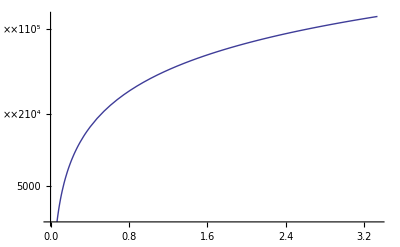

```mathematica
LogPlot[sigmaI1[t],{t,0,mft1}]
```

### Relativistic Gaussian

SN Neutrinos are actually relativistic, so relativistic effects should be considered.

As an approximation, in the direction of momentum, the relativistic contraction is γσ. In the case of neutrinos, energy is E=20MeV, mass can be taken as m=1eV,

```mathematica
gamma1=20 10^6/1
```

20000000

Contraction of width is

```mathematica
sigmaI1R[t_]= sigmaI1[t]/gamma1
```

{(√(1+1.4805×10^49 t^2))/20000000000000000000}

For not small time scale, the result is proportional to time, 192386t.

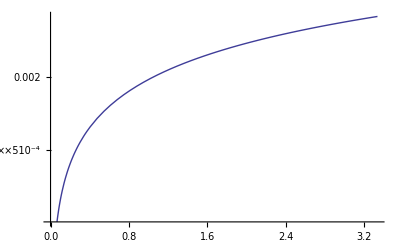

```mathematica
LogPlot[sigmaI1R[t],{t,0,mft1}]
```

## Neutrinos with the same velocity

Some momentum states can have the same velocity even they are form different wave packets.

The velocity for neutrinos can be calculated using this equation: γ m v = p.

```mathematica
Solve[1/(√(1-v^2))m v == p,v];
Grid[{v/.%}]
```

-p/(√(m^2+p^2)) | p/(√(m^2+p^2))

Assume we have neutrino momentum much larger then its mass. p/(√(m^2+p^2))=1/√(m^2/p^2+1). This obviously means the mass doesn’t make any difference. Using Taylor series, we have

```mathematica
Series[1/√(x^2+1),{x,0,3}]
```

1-x^2/2+O[x]^4

The velocity of neutrinos are, to the first order, 1-1/2 m^2/p^2.

Numerically, if we have the heaviest mass eigenstate as m=0.3eV, the largest difference between mass eigenstate for 20MeV neutrinos is

```mathematica
1/2 (0.2)^2/(20 10^6)^2
```

5.×10^-17

This is in unit of speed of light. Then I am going to calculate the value, which is about 10^{-8}m/s~10^7 fm/s. With the impression of the width of the wave packet about 10fm, this is a very large speed.

#### Todo

(It’s really good if I can show how much two wave packets can overlap, which requires some relativistic wave dynamics for an accurate calculation.)
Or not, I can switch to momentum space.